# Discrete Calculus

## 1. Intro

keywords : sequences/series, finite differences, sums/products, gfun
e . g . Finite Sums / Infinite Sums,    Riemann Sums

```mathematica
∑_(k=0)^5 k  
∑_(k=1)^∞ 1/2^k
f[x_]=(x-1)^(1/3); plot=Plot[f[x],{x,0,3},AspectRatio->Automatic,PlotTheme->"Detailed"]
Show[DiscretePlot[f[x],{x,1,3,1/3},ExtentSize->Full],plot]
```

15

1

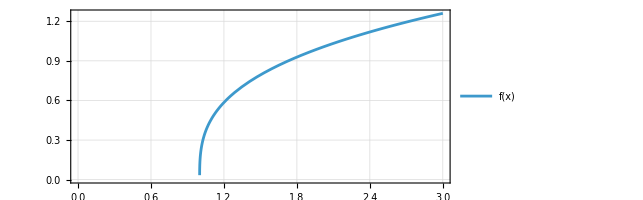

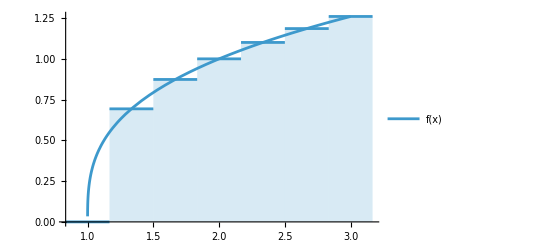

-Graphics-

## Sigma Notation

### Basic Examples

```mathematica
∑_(k=0)^5 k
```

15

### Infinite Sums

```mathematica
∑_(k=1)^∞ 1/2^k
```

1

```mathematica
∑_(k=0)^∞ 1/(k!)
```

ⅇ

## Riemann Sums

```mathematica
f[x_]=(x-1)^(1/3);
plot=Plot[f[x],{x,0,3},AspectRatio->Automatic,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
Show[DiscretePlot[f[x],{x,1,3,1/3},ExtentSize->Full],plot]
```

-Graphics-

```mathematica
N[∑_(k=1)^6 f[1+((3-1)/6)k]*((3-1)/6)]
```

2.03771

## Product Notation

```mathematica
∏_(k=1)^5 k
```

```mathematica
120
```

```mathematica
N[∏_(k=2)^∞ ((k^2-1)/k^2)^(2(k^2-1))((k+1)/(k-1))^k]
```

```mathematica
3.0899225749115415
```

## Taylor Series

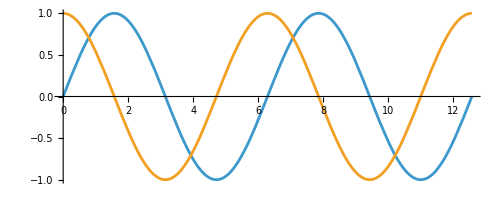

```mathematica
f[x_]=∑_(k=0)^∞ ((-1)^k x^(2k+1))/((2k+1)!);
g[x_]=∑_(k=0)^∞ ((-1)^k x^(2k))/((2k)!);
Plot[{f[x],g[x]},{x,0,4π},AspectRatio->Automatic]
```

```mathematica
f[x_]=x∏_(k=1)^∞ (1-x^2/(k^2 π^2));
g[x_]=∏_(k=1)^∞ (1-(4 x^2)/(π^2(2k-1)^2));
Plot[{f[x],g[x]},{x,0,4π},AspectRatio->Automatic]
```

-Graphics-

## Finite Differences

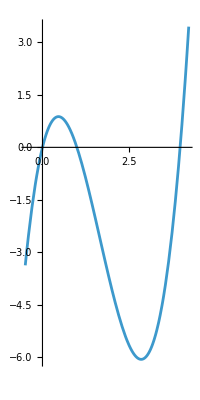

(-4 x+5 x^2-x^3+4 (h+x)-5 (h+x)^2+(h+x)^3)/h

(4 x-5 x^2+x^3-4 (-h+x)+5 (-h+x)^2-(-h+x)^3)/h

(-4 (-a+x)+5 (-a+x)^2-(-a+x)^3+4 (a+x)-5 (a+x)^2+(a+x)^3)/(2 a)

```mathematica
f[x_]=4x-5 x^2+x^3;
plot=Plot[f[x],{x,-0.5,4.25},AspectRatio->Automatic]
difForward[x_,h_]=(f[x+h]-f[x])/h
difBackward[x_,h_]=(f[x]-f[x-h])/h
difCentral[x_,a_]=(f[x+a]-f[x-a])/(2a)
```

```mathematica
(*coding form*)
f'[x]
Limit[difForward[x,h],h->0]
Limit[difBackward[x,h],h->0]
Simplify[Limit[difCentral[x,h],h->0]]
```

4-10 x+3 x^2

4-10 x+3 x^2

4-10 x+3 x^2

«1 more identical outputs»

```mathematica
(*math form*)
f'(x)
difForward(x,h)h0
difBackward(x,h)h0
Simplify[difCentral(x,h)h0]
```

4-10 x+3 x^2

4-10 x+3 x^2

4-10 x+3 x^2

«1 more identical outputs»

## 2. Number Theory

```mathematica
Divisible[10,5]
Mod[12,10](*cannot use %*)
```

True

2

```mathematica
a=420;   (*separate input cell*)
b=860;
```

```mathematica
(*repeat until output appears*)
r=Mod[a,b];
a=b;
If[r>0,b=r,Print[a]];
```

20

```mathematica
(*only need to run once*)
r=Mod[a,b];
a=b;
While[r>0,b=r;r=Mod[a,b];a=b]
Print[a]
```

20

```mathematica
GCD[a,b]
```

20

## 3. Primes

## Basic Things

```mathematica
Table[Prime[i],{i,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
PrimeQ[67]
PrimeQ[267]
CompositeQ[6767]
CompositeQ[673]
```

True

False

True

False

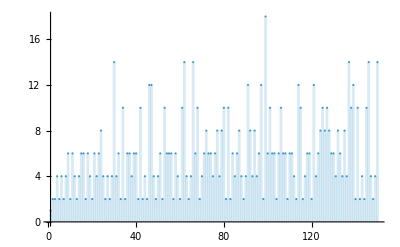

```mathematica
gap[n_]=Prime[n+1]-Prime[n];
DiscretePlot[gap[n],{n,150}]
```

```mathematica
RandomPrime[100]
```

73

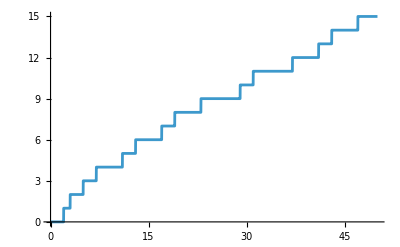

```mathematica
Plot[PrimePi[x],{x,0,50}]
```

## Applications

```mathematica
(*RSA Encryption*)
p=Prime[18];
q=Prime[16];
n=p*q
```

3233

```mathematica
EulerPhi[n]
u=17;
k=15;
CoprimeQ[u,EulerPhi[n]]
PrivKey=(k*EulerPhi[n]+1)/u
```

3120

True

2753

```mathematica
data=ToCharacterCode["Secret"]
encrypted=Mod[data^u,n]
```

{83,101,99,114,101,116}

{2680,1313,281,2412,1313,884}

```mathematica
decrypted=Mod[encrypted^PrivKey,n]
```

{83,101,99,114,101,116}

```mathematica
EulerPhi[n]==(p-1)(q-1)
```

True

## 4. Fibonacci

```mathematica
DiscreteAsymptotic[Fibonacci[n]/Fibonacci[n-1],n->∞]
DiscreteAsymptotic[Fibonacci[n],n->∞]
```

GoldenRatio

GoldenRatio^n/(√5)